# Code used to generate tensors.

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

The following command takes a single integer number and returns a list of 2n variables.

```mathematica
dummyArray=n↦Flatten[(x↦{ToExpression["m"<>ToString[x]],ToExpression["n"<>ToString[x]]})/@Range[n]];
```

This command takes a list of even number of elements, splits it in pairs, and make a metric of each pair.

```mathematica
MTDWrapper=x↦Times@@MTD@@@Partition[x,2];
```

This command takes two lists. The first one is the list to be symmetrized. The second one is a list of two elements. The result is a join list. Its first component it the original list; its second component is a list with the given elements begin swapped.

```mathematica
arraySymmetrization={array,argumets}↦Join[array,(array/.{argumets[[1]]->argumets[[2]],argumets[[2]]->argumets[[1]]})];
```

This is the definition of I tensor. It is taken directly from ArXiV:2201.06812.

```mathematica
ITensor = indexArray↦If[Length[indexArray]≠0,Total[1/2^(Length[indexArray]/2)MTDWrapper/@Function[RotateLeft[#,1]]/@Partition[Fold[arraySymmetrization,indexArray,Partition[indexArray,2]],Length[indexArray]]],1];
```

This is the definition of C tensor. It is taken directly from ArXiV:2201.06812.
For the sake of simplicity (and human-readability) it is realized as a few function.

```mathematica
CTensorStructure={n,kArray,indexArray}↦(-1)^(n+Length[kArray])/(Factorial[Length[kArray]]2^Length[kArray])1/(Times@@kArray)Times@@ITensor/@FoldPairList[TakeDrop,indexArray,2kArray];
kArray={n,m}↦Select[Tuples[Range[n],m],Total[#]==n&];
CTensorCore=indexArray↦Total[Function[Total[Function[CTensorStructure[Length[indexArray]/2,#,indexArray]]/@kArray[Length[indexArray]/2,#]]]/@Range[Length[indexArray]/2]];
CTensor=indexArray↦If[Length[indexArray]≠0,Expand[1/Factorial[Length[indexArray]/2] Total[CTensorCore/@Flatten/@Permutations[Partition[indexArray,2]]]],1];
```

CIII definition. In full analogy with the previous case it is taken from ArXiV:2201.06812; and it is separated in a few function to make human-readable.
Its arguments are made in a very specific form.
CIIITensor[{{μ,ν},{α,β},{ρ,σ}},{m1,n1,....}] -- Here {μ,ν},{α,β}, and {ρ,σ} are external indices that present in √-g g^μν g^αβ g^ρσ. Indices m1,n1,... are internal indices which are contracted with h_{m1n1}....

```mathematica
CIIITensorIndex=indexArray↦FoldPairList[TakeDrop,indexArray,2#]&/@((n↦Select[Tuples[Range[0,n],4],Total[#]==n&])[Length[indexArray]/2]);
CIIITensorStructure={internalIndices,externalIndices}↦Function[{#[[1]],Join[internalIndices[[1]],#[[2]]],Join[internalIndices[[2]],#[[3]]],Join[internalIndices[[3]],#[[4]]]}]/@CIIITensorIndex[externalIndices];
CIIITensorCore={internalIndices,externalIndices}↦Total[Function[(-1)^(Length[externalIndices]/2-Length[#[[1]]]/2)CTensor[#[[1]]]ITensor[#[[2]]]ITensor[#[[3]]]ITensor[#[[4]]]]/@CIIITensorStructure[internalIndices,externalIndices]];
CIIITensor = {internalIndices,externalIndices}↦Expand[1/Factorial[Length[externalIndices]/2] Total[Function[CIIITensorCore[internalIndices,#]]/@Flatten/@Permutations[Partition[externalIndices,2]]]];
```

```mathematica
TTensorGravity={μ,ν,α,β,ρ,σ,λ1,λ2,ρ1,σ1,ρ2,σ2}↦Expand[-MTD[μ,λ1]MTD[ν,λ2]ITensor[{α,β,ρ1,σ1}]ITensor[{ρ,σ,ρ2,σ2}]+MTD[μ,λ1]MTD[ν,λ2]ITensor[{α,ρ,ρ1,σ1}]ITensor[{β,σ,ρ2,σ2}]-2MTD[μ,λ1]MTD[α,λ2]ITensor[{β,ρ,ρ1,σ1}]ITensor[{ν,σ,ρ2,σ2}]+2MTD[μ,λ1]MTD[β,λ2]ITensor[{ν,α,ρ1,σ1}]ITensor[{ρ,σ,ρ2,σ2}]];
GravitonVertexStructure={p1,p2,indexArray}↦Calc[CIIITensor[{{μ1,ν1},{μ2,ν2},{μ3,ν3}},indexArray[[5;;]]]TTensorGravity[Sequence@@Join[Flatten[{ToExpression["μ"<>ToString[#]],ToExpression["ν"<>ToString[#]]}&/@Range[3]],{λ1,λ2},indexArray[[1;;4]]]]FVD[p1,λ1]FVD[p2,λ2]];

GravitonVertexIndex={indexArray}↦Sequence@@{indexArray[[3]],indexArray[[6]],Flatten[Function[#[[1;;2]]]/@Partition[indexArray,3]]};
GravitonVertex=indexArray↦Expand[-ⅈ 2/κ^2 κ^(Length[indexArray]/3)Total[1/Factorial[Length[indexArray]/3] GravitonVertexStructure[GravitonVertexIndex[#]]&/@Flatten/@Permutations[Partition[indexArray,3]]]];
```

```mathematica
GravitonVertex[{a1,b1,q1,a2,b2,q2,a3,b3,q3}]
```

1/6 ⅈ κ q2^a1 q1^a2 g^a3b3 g^b1b2+1/6 ⅈ κ q3^a1 q1^a2 g^a3b3 g^b1b2+1/6 ⅈ κ q3^a1 q2^a2 g^a3b3 g^b1b2+1/6 ⅈ κ q1^a1 q3^a2 g^a3b3 g^b1b2+1/6 ⅈ κ q2^a1 q3^a2 g^a3b3 g^b1b2-1/6 ⅈ κ q2^a1 g^a2b3 q1^a3 g^b1b2-1/6 ⅈ κ q3^a1 g^a2b3 q1^a3 g^b1b2-1/6 ⅈ κ g^a1b3 q3^a2 q1^a3 g^b1b2-1/6 ⅈ κ q3^a1 g^a2b3 q2^a3 g^b1b2-1/6 ⅈ κ g^a1b3 q1^a2 q2^a3 g^b1b2-1/6 ⅈ κ g^a1b3 q3^a2 q2^a3 g^b1b2-1/6 ⅈ κ q2^a1 g^a2a3 q1^b3 g^b1b2-1/6 ⅈ κ q3^a1 g^a2a3 q1^b3 g^b1b2-1/6 ⅈ κ g^a1a3 q3^a2 q1^b3 g^b1b2+1/6 ⅈ κ g^a1a2 q2^a3 q1^b3 g^b1b2+1/6 ⅈ κ g^a1a2 q3^a3 q1^b3 g^b1b2-1/6 ⅈ κ q3^a1 g^a2a3 q2^b3 g^b1b2-1/6 ⅈ κ g^a1a3 q1^a2 q2^b3 g^b1b2-1/6 ⅈ κ g^a1a3 q3^a2 q2^b3 g^b1b2+1/6 ⅈ κ g^a1a2 q1^a3 q2^b3 g^b1b2+1/6 ⅈ κ g^a1a2 q3^a3 q2^b3 g^b1b2+1/6 ⅈ κ g^a1a2 q1^a3 q3^b3 g^b1b2+1/6 ⅈ κ g^a1a2 q2^a3 q3^b3 g^b1b2+1/6 ⅈ κ g^a1b3 g^a2a3 (q1·q2) g^b1b2+1/6 ⅈ κ g^a1a3 g^a2b3 (q1·q2) g^b1b2-1/6 ⅈ κ g^a1a2 g^a3b3 (q1·q2) g^b1b2+1/6 ⅈ κ g^a1b3 g^a2a3 (q1·q3) g^b1b2+1/6 ⅈ κ g^a1a3 g^a2b3 (q1·q3) g^b1b2-1/3 ⅈ κ g^a1a2 g^a3b3 (q1·q3) g^b1b2+1/6 ⅈ κ g^a1b3 g^a2a3 (q2·q3) g^b1b2+1/6 ⅈ κ g^a1a3 g^a2b3 (q2·q3) g^b1b2-1/3 ⅈ κ g^a1a2 g^a3b3 (q2·q3) g^b1b2-1/6 ⅈ κ q2^a1 q1^a2 g^a3b2 g^b1b3-1/6 ⅈ κ q3^a1 q1^a2 g^a3b2 g^b1b3-1/6 ⅈ κ q2^a1 q3^a2 g^a3b2 g^b1b3+1/6 ⅈ κ q2^a1 g^a2b2 q1^a3 g^b1b3+1/6 ⅈ κ q3^a1 g^a2b2 q1^a3 g^b1b3-1/6 ⅈ κ g^a1b2 q3^a2 q1^a3 g^b1b3+1/6 ⅈ κ q1^a1 g^a2b2 q2^a3 g^b1b3+1/6 ⅈ κ q3^a1 g^a2b2 q2^a3 g^b1b3-1/6 ⅈ κ g^a1b2 q1^a2 q2^a3 g^b1b3-1/6 ⅈ κ g^a1b2 q3^a2 q2^a3 g^b1b3+1/6 ⅈ κ q2^a1 g^a2b2 q3^a3 g^b1b3+1/6 ⅈ κ q2^a1 g^a2b3 g^a3b2 q1^b1+1/6 ⅈ κ q3^a1 g^a2b3 g^a3b2 q1^b1-1/6 ⅈ κ q2^a1 g^a2b2 g^a3b3 q1^b1-1/6 ⅈ κ q3^a1 g^a2b2 g^a3b3 q1^b1+1/6 ⅈ κ g^a1b2 q3^a2 g^a3b3 q1^b1+1/6 ⅈ κ g^a1b3 g^a2b2 q2^a3 q1^b1+1/6 ⅈ κ q1^a1 g^a2b3 g^a3b2 q2^b1+1/6 ⅈ κ q3^a1 g^a2b3 g^a3b2 q2^b1-1/6 ⅈ κ g^a1b3 q1^a2 g^a3b2 q2^b1-1/6 ⅈ κ g^a1b3 q3^a2 g^a3b2 q2^b1-1/6 ⅈ κ q1^a1 g^a2b2 g^a3b3 q2^b1-1/3 ⅈ κ q3^a1 g^a2b2 g^a3b3 q2^b1+1/6 ⅈ κ g^a1b2 q1^a2 g^a3b3 q2^b1+1/6 ⅈ κ g^a1b2 q3^a2 g^a3b3 q2^b1+1/6 ⅈ κ g^a1b3 g^a2b2 q1^a3 q2^b1-1/6 ⅈ κ g^a1b2 g^a2b3 q1^a3 q2^b1+1/6 ⅈ κ g^a1b3 g^a2b2 q3^a3 q2^b1+1/6 ⅈ κ q1^a1 g^a2b3 g^a3b2 q3^b1+1/6 ⅈ κ q2^a1 g^a2b3 g^a3b2 q3^b1-1/6 ⅈ κ g^a1b3 q1^a2 g^a3b2 q3^b1-1/6 ⅈ κ q1^a1 g^a2b2 g^a3b3 q3^b1-1/3 ⅈ κ q2^a1 g^a2b2 g^a3b3 q3^b1+1/6 ⅈ κ g^a1b2 q1^a2 g^a3b3 q3^b1+1/6 ⅈ κ g^a1b2 q2^a2 g^a3b3 q3^b1+1/6 ⅈ κ g^a1b3 g^a2b2 q1^a3 q3^b1-1/6 ⅈ κ g^a1b2 g^a2b3 q1^a3 q3^b1+1/6 ⅈ κ g^a1b3 g^a2b2 q2^a3 q3^b1-1/6 ⅈ κ g^a1b2 g^a2b3 q2^a3 q3^b1-1/6 ⅈ κ q2^a1 q1^a2 g^a3b1 g^b2b3-1/6 ⅈ κ q3^a1 q1^a2 g^a3b1 g^b2b3-1/6 ⅈ κ q2^a1 q3^a2 g^a3b1 g^b2b3-1/6 ⅈ κ q2^a1 g^a2b1 q1^a3 g^b2b3-1/6 ⅈ κ q3^a1 g^a2b1 q1^a3 g^b2b3+1/6 ⅈ κ g^a1b1 q2^a2 q1^a3 g^b2b3+1/6 ⅈ κ g^a1b1 q3^a2 q1^a3 g^b2b3-1/6 ⅈ κ q3^a1 g^a2b1 q2^a3 g^b2b3+1/6 ⅈ κ g^a1b1 q1^a2 q2^a3 g^b2b3+1/6 ⅈ κ g^a1b1 q3^a2 q2^a3 g^b2b3+1/6 ⅈ κ g^a1b1 q1^a2 q3^a3 g^b2b3+1/6 ⅈ κ q2^a1 g^a2a3 q1^b1 g^b2b3+1/6 ⅈ κ q3^a1 g^a2a3 q1^b1 g^b2b3+1/6 ⅈ κ q1^a1 g^a2a3 q2^b1 g^b2b3+1/6 ⅈ κ q3^a1 g^a2a3 q2^b1 g^b2b3-1/6 ⅈ κ g^a1a3 q1^a2 q2^b1 g^b2b3-1/6 ⅈ κ g^a1a3 q3^a2 q2^b1 g^b2b3-1/6 ⅈ κ g^a1a2 q1^a3 q2^b1 g^b2b3+1/6 ⅈ κ q1^a1 g^a2a3 q3^b1 g^b2b3+1/6 ⅈ κ q2^a1 g^a2a3 q3^b1 g^b2b3-1/6 ⅈ κ g^a1a3 q1^a2 q3^b1 g^b2b3-1/6 ⅈ κ g^a1a2 q1^a3 q3^b1 g^b2b3-1/6 ⅈ κ g^a1a2 q2^a3 q3^b1 g^b2b3-1/6 ⅈ κ q2^a1 g^a2b3 g^a3b1 q1^b2-1/6 ⅈ κ q3^a1 g^a2b3 g^a3b1 q1^b2+1/6 ⅈ κ g^a1b3 q2^a2 g^a3b1 q1^b2+1/6 ⅈ κ g^a1b3 q3^a2 g^a3b1 q1^b2+1/6 ⅈ κ q2^a1 g^a2b1 g^a3b3 q1^b2+1/6 ⅈ κ q3^a1 g^a2b1 g^a3b3 q1^b2-1/6 ⅈ κ g^a1b1 q2^a2 g^a3b3 q1^b2-1/3 ⅈ κ g^a1b1 q3^a2 g^a3b3 q1^b2-1/6 ⅈ κ g^a1b3 g^a2b1 q2^a3 q1^b2+1/6 ⅈ κ g^a1b1 g^a2b3 q2^a3 q1^b2+1/6 ⅈ κ g^a1b1 g^a2b3 q3^a3 q1^b2-1/6 ⅈ κ q2^a1 g^a2a3 g^b1b3 q1^b2-1/6 ⅈ κ q3^a1 g^a2a3 g^b1b3 q1^b2+1/6 ⅈ κ g^a1a3 q2^a2 g^b1b3 q1^b2+1/6 ⅈ κ g^a1a3 q3^a2 g^b1b3 q1^b2-1/6 ⅈ κ g^a1a2 q2^a3 g^b1b3 q1^b2-1/6 ⅈ κ g^a1b3 g^a2a3 q2^b1 q1^b2-1/6 ⅈ κ g^a1a3 g^a2b3 q2^b1 q1^b2+1/6 ⅈ κ g^a1a2 g^a3b3 q2^b1 q1^b2-1/6 ⅈ κ g^a1b3 g^a2a3 q3^b1 q1^b2-1/6 ⅈ κ g^a1a3 g^a2b3 q3^b1 q1^b2+1/6 ⅈ κ g^a1a2 g^a3b3 q3^b1 q1^b2+1/6 ⅈ κ g^a1b3 q1^a2 g^a3b1 q2^b2+1/6 ⅈ κ g^a1b3 q3^a2 g^a3b1 q2^b2+1/6 ⅈ κ q3^a1 g^a2b1 g^a3b3 q2^b2-1/6 ⅈ κ g^a1b1 q1^a2 g^a3b3 q2^b2-1/6 ⅈ κ g^a1b1 q3^a2 g^a3b3 q2^b2+1/6 ⅈ κ g^a1b1 g^a2b3 q1^a3 q2^b2+1/6 ⅈ κ g^a1a3 q1^a2 g^b1b3 q2^b2+1/6 ⅈ κ g^a1a3 q3^a2 g^b1b3 q2^b2+1/6 ⅈ κ g^a1a2 g^a3b3 q3^b1 q2^b2-1/6 ⅈ κ q2^a1 g^a2b3 g^a3b1 q3^b2+1/6 ⅈ κ g^a1b3 q1^a2 g^a3b1 q3^b2+1/6 ⅈ κ g^a1b3 q2^a2 g^a3b1 q3^b2+1/6 ⅈ κ q1^a1 g^a2b1 g^a3b3 q3^b2+1/6 ⅈ κ q2^a1 g^a2b1 g^a3b3 q3^b2-1/3 ⅈ κ g^a1b1 q1^a2 g^a3b3 q3^b2-1/6 ⅈ κ g^a1b1 q2^a2 g^a3b3 q3^b2-1/6 ⅈ κ g^a1b3 g^a2b1 q1^a3 q3^b2+1/6 ⅈ κ g^a1b1 g^a2b3 q1^a3 q3^b2-1/6 ⅈ κ g^a1b3 g^a2b1 q2^a3 q3^b2+1/6 ⅈ κ g^a1b1 g^a2b3 q2^a3 q3^b2-1/6 ⅈ κ q2^a1 g^a2a3 g^b1b3 q3^b2+1/6 ⅈ κ g^a1a3 q1^a2 g^b1b3 q3^b2+1/6 ⅈ κ g^a1a3 q2^a2 g^b1b3 q3^b2-1/6 ⅈ κ g^a1a2 q1^a3 g^b1b3 q3^b2-1/6 ⅈ κ g^a1a2 q2^a3 g^b1b3 q3^b2+1/6 ⅈ κ g^a1a2 g^a3b3 q1^b1 q3^b2-1/6 ⅈ κ g^a1b3 g^a2a3 q2^b1 q3^b2-1/6 ⅈ κ g^a1a3 g^a2b3 q2^b1 q3^b2+1/6 ⅈ κ g^a1a2 g^a3b3 q2^b1 q3^b2+1/6 ⅈ κ q2^a1 g^a2b2 g^a3b1 q1^b3+1/6 ⅈ κ q3^a1 g^a2b2 g^a3b1 q1^b3-1/6 ⅈ κ g^a1b2 q3^a2 g^a3b1 q1^b3-1/6 ⅈ κ q2^a1 g^a2b1 g^a3b2 q1^b3-1/6 ⅈ κ q3^a1 g^a2b1 g^a3b2 q1^b3+1/6 ⅈ κ g^a1b1 q2^a2 g^a3b2 q1^b3+1/6 ⅈ κ g^a1b1 q3^a2 g^a3b2 q1^b3+1/6 ⅈ κ g^a1b2 g^a2b1 q2^a3 q1^b3-1/3 ⅈ κ g^a1b1 g^a2b2 q2^a3 q1^b3+1/6 ⅈ κ g^a1b2 g^a2b1 q3^a3 q1^b3-1/6 ⅈ κ g^a1b1 g^a2b2 q3^a3 q1^b3-1/6 ⅈ κ g^a1b2 g^a2a3 q2^b1 q1^b3+1/6 ⅈ κ g^a1a3 g^a2b2 q2^b1 q1^b3-1/6 ⅈ κ g^a1a2 g^a3b2 q2^b1 q1^b3-1/6 ⅈ κ g^a1b2 g^a2a3 q3^b1 q1^b3+1/6 ⅈ κ g^a1a3 g^a2b2 q3^b1 q1^b3-1/6 ⅈ κ g^a1a2 g^a3b2 q3^b1 q1^b3+1/6 ⅈ κ g^a1b1 g^a2a3 q2^b2 q1^b3+1/6 ⅈ κ g^a1b1 g^a2a3 q3^b2 q1^b3-1/6 ⅈ κ g^a1a3 g^a2b1 q3^b2 q1^b3-1/6 ⅈ κ g^a1a2 g^a3b1 q3^b2 q1^b3+1/6 ⅈ κ q1^a1 g^a2b2 g^a3b1 q2^b3+1/6 ⅈ κ q3^a1 g^a2b2 g^a3b1 q2^b3-1/6 ⅈ κ g^a1b2 q1^a2 g^a3b1 q2^b3-1/6 ⅈ κ g^a1b2 q3^a2 g^a3b1 q2^b3-1/6 ⅈ κ q3^a1 g^a2b1 g^a3b2 q2^b3+1/6 ⅈ κ g^a1b1 q1^a2 g^a3b2 q2^b3+1/6 ⅈ κ g^a1b1 q3^a2 g^a3b2 q2^b3+1/6 ⅈ κ g^a1b2 g^a2b1 q1^a3 q2^b3-1/3 ⅈ κ g^a1b1 g^a2b2 q1^a3 q2^b3+1/6 ⅈ κ g^a1b2 g^a2b1 q3^a3 q2^b3-1/6 ⅈ κ g^a1b1 g^a2b2 q3^a3 q2^b3+1/6 ⅈ κ g^a1a3 g^a2b2 q1^b1 q2^b3-1/6 ⅈ κ g^a1b2 g^a2a3 q3^b1 q2^b3+1/6 ⅈ κ g^a1a3 g^a2b2 q3^b1 q2^b3-1/6 ⅈ κ g^a1a2 g^a3b2 q3^b1 q2^b3+1/6 ⅈ κ g^a1b1 g^a2a3 q1^b2 q2^b3-1/6 ⅈ κ g^a1a3 g^a2b1 q1^b2 q2^b3-1/6 ⅈ κ g^a1a2 g^a3b1 q1^b2 q2^b3+1/6 ⅈ κ g^a1b1 g^a2a3 q3^b2 q2^b3-1/6 ⅈ κ g^a1a3 g^a2b1 q3^b2 q2^b3-1/6 ⅈ κ g^a1a2 g^a3b1 q3^b2 q2^b3+1/6 ⅈ κ q2^a1 g^a2b2 g^a3b1 q3^b3+1/6 ⅈ κ g^a1b1 q1^a2 g^a3b2 q3^b3+1/6 ⅈ κ g^a1b2 g^a2b1 q1^a3 q3^b3-1/6 ⅈ κ g^a1b1 g^a2b2 q1^a3 q3^b3+1/6 ⅈ κ g^a1b2 g^a2b1 q2^a3 q3^b3-1/6 ⅈ κ g^a1b1 g^a2b2 q2^a3 q3^b3+1/6 ⅈ κ g^a1a3 g^a2b2 q2^b1 q3^b3+1/6 ⅈ κ g^a1b1 g^a2a3 q1^b2 q3^b3-1/3 ⅈ κ g^a1b3 g^a2b2 g^a3b1 (q1·q2)+1/6 ⅈ κ g^a1b2 g^a2b3 g^a3b1 (q1·q2)+1/6 ⅈ κ g^a1b3 g^a2b1 g^a3b2 (q1·q2)-1/3 ⅈ κ g^a1b1 g^a2b3 g^a3b2 (q1·q2)-1/6 ⅈ κ g^a1b2 g^a2b1 g^a3b3 (q1·q2)+1/3 ⅈ κ g^a1b1 g^a2b2 g^a3b3 (q1·q2)+1/6 ⅈ κ g^a1b2 g^a2a3 g^b1b3 (q1·q2)-1/3 ⅈ κ g^a1a3 g^a2b2 g^b1b3 (q1·q2)+1/6 ⅈ κ g^a1a2 g^a3b2 g^b1b3 (q1·q2)-1/3 ⅈ κ g^a1b1 g^a2a3 g^b2b3 (q1·q2)+1/6 ⅈ κ g^a1a3 g^a2b1 g^b2b3 (q1·q2)+1/6 ⅈ κ g^a1a2 g^a3b1 g^b2b3 (q1·q2)-1/6 ⅈ κ g^a1b3 g^a2b2 g^a3b1 (q1·q3)+1/6 ⅈ κ g^a1b2 g^a2b3 g^a3b1 (q1·q3)+1/6 ⅈ κ g^a1b3 g^a2b1 g^a3b2 (q1·q3)-1/3 ⅈ κ g^a1b1 g^a2b3 g^a3b2 (q1·q3)-1/3 ⅈ κ g^a1b2 g^a2b1 g^a3b3 (q1·q3)+1/3 ⅈ κ g^a1b1 g^a2b2 g^a3b3 (q1·q3)+1/6 ⅈ κ g^a1b2 g^a2a3 g^b1b3 (q1·q3)-1/6 ⅈ κ g^a1a3 g^a2b2 g^b1b3 (q1·q3)+1/6 ⅈ κ g^a1a2 g^a3b2 g^b1b3 (q1·q3)-1/3 ⅈ κ g^a1b1 g^a2a3 g^b2b3 (q1·q3)+1/6 ⅈ κ g^a1a3 g^a2b1 g^b2b3 (q1·q3)+1/6 ⅈ κ g^a1a2 g^a3b1 g^b2b3 (q1·q3)-1/3 ⅈ κ g^a1b3 g^a2b2 g^a3b1 (q2·q3)+1/6 ⅈ κ g^a1b2 g^a2b3 g^a3b1 (q2·q3)+1/6 ⅈ κ g^a1b3 g^a2b1 g^a3b2 (q2·q3)-1/6 ⅈ κ g^a1b1 g^a2b3 g^a3b2 (q2·q3)-1/3 ⅈ κ g^a1b2 g^a2b1 g^a3b3 (q2·q3)+1/3 ⅈ κ g^a1b1 g^a2b2 g^a3b3 (q2·q3)+1/6 ⅈ κ g^a1b2 g^a2a3 g^b1b3 (q2·q3)-1/3 ⅈ κ g^a1a3 g^a2b2 g^b1b3 (q2·q3)+1/6 ⅈ κ g^a1a2 g^a3b2 g^b1b3 (q2·q3)-1/6 ⅈ κ g^a1b1 g^a2a3 g^b2b3 (q2·q3)+1/6 ⅈ κ g^a1a3 g^a2b1 g^b2b3 (q2·q3)+1/6 ⅈ κ g^a1a2 g^a3b1 g^b2b3 (q2·q3)

# Timings. Do not run without a necessity.

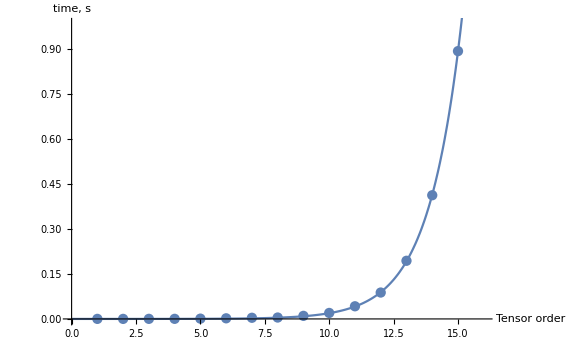

```mathematica
Table[Timing[ITensor[dummyArray[i]]][[1]],{i,1,15}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

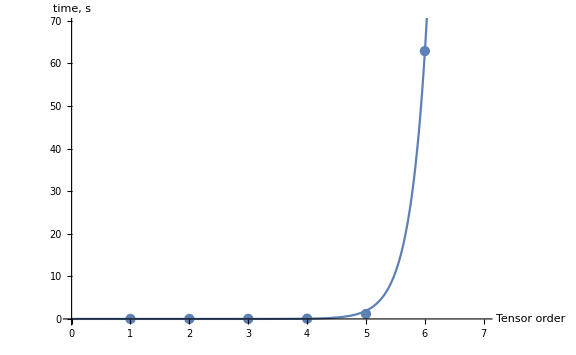

```mathematica
Table[Timing[CTensor[dummyArray[i]]][[1]],{i,1,6}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
```

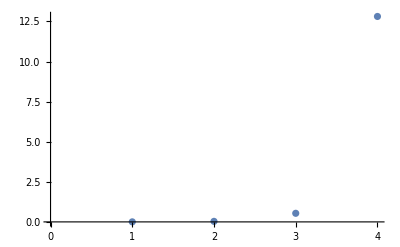

```mathematica
ListPlot[Table[Timing[CIIITensor[dummyArray[i]]][[1]],{i,3,6}]]
```

# Export

## Code

```mathematica
exportITensor[order_]:=Module[{cursor},
Print["Export of I tensors is initiated."];
For[cursor=1,cursor≤order,cursor++,
ITensor[dummyArray[cursor]]>>"ITensor_"<>ToString[cursor];
Print["Done for order "<>ToString[cursor]];
]
]
```

```mathematica
exportCTensor[order_]:=Module[{cursor},
Print["Export of C tensors is initiated."];
For[cursor=1,cursor≤order,cursor++,
CTensor[dummyArray[cursor]]>>"CTensor_"<>ToString[cursor];
Print["Done for order "<>ToString[cursor]];
]
]
```

```mathematica
exportITensor[5]
exportCTensor[5]
```

Export of I tensors is initiated.

Done for order 1

Done for order 2

Done for order 3

Done for order 4

Done for order 5

Export of C tensors is initiated.

Done for order 1

Done for order 2

Done for order 3

Done for order 4

Done for order 5

```mathematica
exportGravitonVertex[order_] := Module[{cursor}, 
If[order<3,Print["The order must be three or higher!"];Return[]];
Print["Export of graviton vertices is initiated."];
For[cursor=3,cursor≤order,cursor++,
Evaluate[GravitonVertex[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]],ToExpression["p"<>ToString[#]]}]/@Range[cursor]]]]>>"GravitonVertex_"<>ToString[cursor];
Print["Done for order "<>ToString[cursor]];
]
]
```

```mathematica
exportGravitonVertex[4]
```

Export of graviton vertices is initiated.

Done for order 3